```mathematica
TransformationM[zeta_, CamPoints_]:=Module[{PiKc,KPoints,p1,p2,p3,p4},
PiKc={{zeta,0,0,0},{0,zeta,0,0},{0,0,zeta,0},{0,0,1,0}};
KPoints=PiKc.CamPoints;

Print["K1Points with zeta matrix"];
Print[ MatrixForm[KPoints]];

KPoints[[All,1]] = KPoints[[All,1]]/KPoints[[4,1]];
KPoints[[All,2]] = KPoints[[All,2]]/KPoints[[4,2]];
KPoints[[All,3]]= KPoints[[All,3]]/KPoints[[4,3]];
KPoints[[All,4]]= KPoints[[All,4]]/KPoints[[4,4]];

Print["FinalPoints"];
Print[ MatrixForm[Rationalize[N[KPoints]]]];

CameraToImage[KPoints ];

p1= KPoints[[1;;2,1]];
p2 =KPoints[[1;;2,2]];
p3=KPoints[[1;;2,3]];
p4=KPoints[[1;;2,4]];

Print[Show[Graphics[{Thick,Blue,PointSize[0.02],Point[{p1}]}], Graphics[{Thick,Blue,PointSize[0.02],Point[{p2}]}],Graphics[{Thick,Blue, PointSize[0.02],Point[{p3}]}],Graphics[{Thick,Blue, PointSize[0.02],Point[{p4}]}]]];
(*Retun[p1,p2,p3,p4];*)

];
```

```mathematica
RotationsTranlationE1[alpha_,Mx_,My_,Mz_]:=Module[{Re1},
Re1= {{1,0,0,Mx},{0,Cos[alpha Degree], -Sin[alpha Degree],0,My}, {0,Sin[alpha Degree],Cos[alpha Degree],Mz}{0,0,0,1}};
Return[Re1]
];

RotationsTranlationE2[alpha_,Mx_,My_,Mz_]:=Module[{Re2},
Re2 = {{Cos[alpha Degree],0,Sin[alpha Degree],Mx},{0,1,0,My},{-Sin[alpha Degree],0, Cos[alpha Degree],Mz},{0,0,0,1}};
Return[Re2]
];

RotationsTranlationE3[alpha_,Mx_,My_,Mz_]:=Module[{Re3},
Re3 = {{Cos[alpha Degree],-Sin[alpha Degree],0,Mx},{Sin[alpha Degree], Cos[alpha Degree],0,My},{0,0,1,0},{0,0,0,1}};
Return[Re3]
];
```

```mathematica
WorldToCamera[Aw_,Bw_,Cw_,Dw_,T1_]:=Module[{T2,T3, Ak,Bk,Ck,Dk,  CamPoints},
Print[MatrixForm[T1]];

Ak = T1.Aw;
Bk = T1.Bw;
Ck = T1.Cw;
Dk = T1.Dw;

CamPoints= {{Ak[[1]], Bk[[1]], Ck[[1]], Dk[[1]]},{Ak[[2]], Bk[[2]], Ck[[2]], Dk[[2]]},{Ak[[3]], Bk[[3]], Ck[[3]], Dk[[3]]},{Ak[[4]], Bk[[4]], Ck[[4]], Dk[[4]]}};

Retun[CamPoints];

Print["CamPoints"];
Print[MatrixForm[CamPoints]];

TransformationM[zeta,CamPoints];
];
```

```mathematica
CameraToImage[KPoints_]:=Module[{Ab,Bb,Cb,Db},
(*Tb ist hier so gewählt das der Urspung der Kamera mit dem Ursprung des Sensors übereinstimmt, normal müsste es hier noch eine Translation des Urspungs geben*)

Print["ImagePoints A,B,C,D"];

Ab= KPoints[[All,1]].Tb;
Bb= KPoints[[All,2]].Tb;
Cb= KPoints[[All,3]].Tb;
Db= KPoints[[All,4]].Tb;

Print[ MatrixForm[Rationalize[N[Ab]]]];
Print[ MatrixForm[Rationalize[N[Bb]]]];
Print[ MatrixForm[Rationalize[N[Cb]]]];
Print[ MatrixForm[Rationalize[N[Db]]]];

];
```

```mathematica
Aw = {0,0,2,1};
```

```mathematica
Bw={1,0,2,1};
```

```mathematica
Cw={1,1,2,1};
```

```mathematica
Dw = {0,1,2,1};

zeta = -1;

T1=RotationsTranlationE3[180,0,0,0];
```

```mathematica
T2=RotationsTranlationE2[45,0,0,0].T1;

Tb= {{1,0,0},{0,1,0},{0,0,-1},{0,0,1}};
```

```mathematica
WorldToCamera[Aw,Bw,Cw,Dw,T1]
```

(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

CamPoints

(0 | -1 | -1 | 0
0 | 0 | -1 | -1
2 | 2 | 2 | 2
1 | 1 | 1 | 1)

K1Points with zeta matrix

(0 | 1 | 1 | 0
0 | 0 | 1 | 1
-2 | -2 | -2 | -2
2 | 2 | 2 | 2)

FinalPoints

(0 | 1/2 | 1/2 | 0
0 | 0 | 1/2 | 1/2
-1 | -1 | -1 | -1
1 | 1 | 1 | 1)

ImagePoints A,B,C,D

(0
0
2)

(1/2
0
2)

(1/2
1/2
2)

(0
1/2
2)

-Graphics-

(-1/(√2) | 0 | 1/(√2) | 0
0 | -1 | 0 | 0
1/(√2) | 0 | 1/(√2) | 0
0 | 0 | 0 | 1)

CamPoints

(√2 | -1/(√2)+√2 | -1/(√2)+√2 | √2
0 | 0 | -1 | -1
√2 | 1/(√2)+√2 | 1/(√2)+√2 | √2
1 | 1 | 1 | 1)

K1Points with zeta matrix

(-√2 | 1/(√2)-√2 | 1/(√2)-√2 | -√2
0 | 0 | 1 | 1
-√2 | -1/(√2)-√2 | -1/(√2)-√2 | -√2
√2 | 1/(√2)+√2 | 1/(√2)+√2 | √2)

FinalPoints

(-1 | -1/3 | -1/3 | -1
0 | 0 | 0.471405 | 0.707107
-1 | -1 | -1 | -1
1 | 1 | 1 | 1)

ImagePoints A,B,C,D

(-1
0
2)

(-1/3
0
2)

(-1/3
0.471405
2)

(-1
0.707107
2)

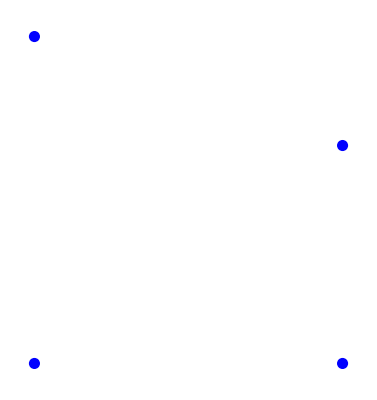

```mathematica
WorldToCamera[Aw,Bw,Cw,Dw,T2]
```